```mathematica
Clear["Global`*"]
Needs["Cosmology`Defs`"]
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Cosmology tests

```mathematica
setCosmo[om_, h_] := Join[{OmegaMh2-> om h^2, OmegaDEh2-> (1-om)h^2}, FoMSWG]//
	DeleteDuplicates[#, #1[[1]]==#2[[1]] &] &
```

```mathematica
FoMSWG
```

{Omegabh2→0.0227,OmegaMh2→0.1326,OmegaKh2→0.,OmegaDEh2→0.3844,ns→0.963,w0→-1.,wa→0.,TCMB→2.726,gamma→0.55}

```mathematica
jpcosmo = setCosmo[0.274, 0.7]
```

{OmegaMh2→0.13426,OmegaDEh2→0.35574,Omegabh2→0.0227,OmegaKh2→0.,ns→0.963,w0→-1.,wa→0.,TCMB→2.726,gamma→0.55}

```mathematica
(* Tests to make sure we get the same values as John *)
(* z=0.1:293.67781630423769, z=0.4:1094.911478642548 *)
comdis[z2a[#], jpcosmo]*3000.0*Hubble[1,jpcosmo]& /@ {0.1,0.4}
```

{293.692,1094.99}

## Redshift distributions

```mathematica
Clear[lowznz, lowznzdat];lowznzdat = Import["../data/boss/LOWZ-north-Nz.dat","Table"]//Last;
lowzinvCDF[z_]:= Module[{xmap},
xmap = 2*z-1;
Plus@@MapThread[#1 ChebyshevT[#2-1,xmap]&,{lowznzdat, Range@Length@lowznzdat}]
];
```

```mathematica
lowzinvCDF[{0.05,0.6}]
```

{0.0906279,0.333532}

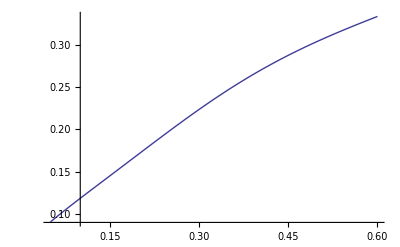

```mathematica
Plot[lowzinvCDF[z],{z,0.05,0.6}]
```

```mathematica
lowzcdf = Interpolation[Table[{lowzinvCDF[x],x},{x,0,1,0.001}]];
lowzPDF = lowzcdf';
```

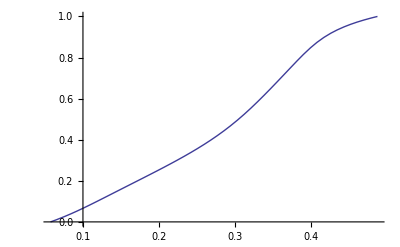

```mathematica
Plot[lowzcdf[z], {z, lowzinvCDF[0], lowzinvCDF[1]}]
```

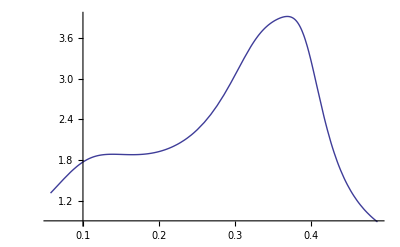

```mathematica
Plot[lowzPDF[z],{z,lowzinvCDF[0], lowzinvCDF[1]}]
```

```mathematica
lowzPDF[
```